```mathematica
f[x_]=x^2*(Log[x-√(x^2-2)]+Log[x])
```

x^2 (Log[x]+Log[x-√(-2+x^2)])

```mathematica
Limit[f[x],x->Infinity]
```

1/2

```mathematica
a[n_]=If[n==1,2,√(5+2*a[n-1])]
```

If[n==1,2,√(5+2 a[n-1])]

```mathematica
Table[N[a[n],15],{n,1,50}]
```

{2.,3.,3.3166247903554,3.41075498690698,3.43824227968506,3.44622758380379,3.44854391991861,3.44921553977672,3.44941025097819,3.44946669819501,3.44948306219787,3.44948780609466,3.4494891813411,3.44948958002227,3.44948969559912,3.44948972910462,3.44948973881779,3.44948974163362,3.44948974244992,3.44948974268657,3.44948974275517,3.44948974277506,3.44948974278082,3.4494897427825,3.44948974278298,3.44948974278312,3.44948974278316,3.44948974278317,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318,3.44948974278318}

```mathematica
a[16]
```

√(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √(5+2 √11)))))))))))))

```mathematica
N[%,15]
```

3.44948972910462

```mathematica
Limit[a[n],n->Infinity]
```

lim_(n→∞) If[n==1,2,√(5+2 a[n-1])]

```mathematica
Lim[√(5+2a[n-1]),n->Infinity]
```

Lim[√(5+2 a[-1+n]),n→∞]

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[1]==2, a[n+1]==√(5+2a[n])},a[n],n]
```

RSolve[{a[1]==2,a[1+n]==√(5+2 a[n])},a[n],n]

```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=N[(an+bn)/2,20];
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

```mathematica
b[x_]=x^7-123
```

-123+x^7

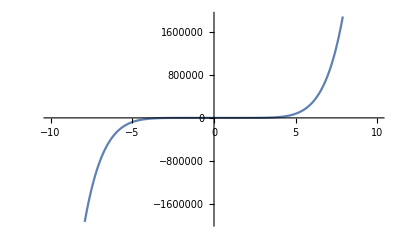

```mathematica
Plot [b[x],{x,-10,10}]
```

```mathematica
Biseccio[b,{-5,5,40}]
```

1.9886477952695713611

```mathematica
N[Log[(10^11)*10] / Log[2]]
```

39.8631

```mathematica
∑_(n=1)^Infinity ((-1)^(n+1)*((2n^2)+5))/n^4
```

1/144 π^2 (24+7 π^2)

```mathematica
N[1/144 π^2 (24+7 π^2)]
```

6.3801

```mathematica
Reduce[(2*(n+1)^2+5)/(n+1)^4<10^-4]
```

n<Root-142.Root[-69999-39996 #1-19994 #1^2+4 #1^3+#1^4&,1]-142.43019369136883||n>Root140.Root[-69999-39996 #1-19994 #1^2+4 #1^3+#1^4&,2]140.4301936913688

```mathematica
N[%]
```

n<-142.43||n>140.43

```mathematica
∑_(n=1)^141 (((-1)^(n+1))*((2*n^2)+5))/n^4
```

1571452181388880909007274232592100370598469503781514138659765304994243782409306205130177722842245979309482871342532203974219395153418882998260182830192197322027338432628381801986877641570146106407229677668211898624719141381907818895638482990144271/246303399420818672067944315265251273554399442165763971820241045597981021893682248059360360711837611790102247760361257515407347176545625071863158806294477484535539247898926996881619464358758111106958005621919935920171792387265530966835200000000000

```mathematica
N[%]
```

6.38005

```mathematica
N[1/144 π^2 (24+7*π^2)]
```

6.3801

```mathematica
RSolve[{a[0]==-3,a[1]==-2,a[n+2]==a[n+1]-14a[n]+5n},a[n],n]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -1022==1.

Hold[RSolve[{a[0]==-3,a[1]==-2,a[n+2]==a[n+1]-14 a[n]+5 n},a[n],n]]

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[0]==-3,a[1]==-2,a[n+2]==9*a[n+1]-14a[n]+5n},a[n],n]
```

{{a[n]→1/180 (175-27 2^(5+n)+149 7^n+150 n)}}